/Users/zack/Documents/oscillators/snakingoscillators

-Graphics-

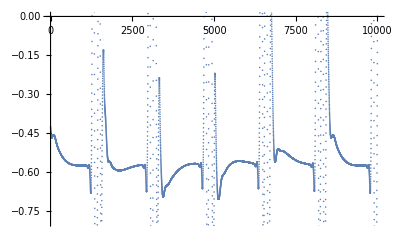

{{1311},{1312},{1313},{1483},{1484},{1485},{3015},{3016},{3017},{3208},{3209},{4728},{4729},{4730},{4731},{4912},{4913},{4914},{6444},{6445},{6446},{6447},{6581},{6582},{6583},{6584},{6585},{8155},{8156},{8157},{8302},{8303},{9858},{9859},{9860},{9861}}

```mathematica
SetDirectory[NotebookDirectory[]]
filebase="data/test4";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
Grid[{{ListDensityPlot[theta,AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->{-Pi,Pi},ColorFunctionScaling->False],ListDensityPlot[phi,AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->{-Pi,Pi},ColorFunctionScaling->False],ListPlot[Transpose[{Cos[phi[[All,1]]],Cos[theta[[All,1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]}}]
ListPlot[Partition[dat,4*M][[All,1]]]
Position[Partition[dat,4*M][[All,1]],u_/;u>0.999]
```

```mathematica
out=Partition[dat,4*M][[2126;;5211]];
Manipulate[ListPlot[{ArcTan[out[[n,1;;M]],out[[n,M+1;;2*M]]],ArcTan[out[[n,2*M+1;;3*M]],out[[n,3*M+1;;4*M]]]},PlotRange->{-Pi,Pi}],{n,1,Length[out],1}]
Export["data/chimera2.dat",Table[Prepend[out[[i]],0.1*(i-1)],{i,1,Length[out]}]]
```

data/chimera2.dat

```mathematica
vals=(#/#[[1]]&@Flatten[{#[[1;;M]]+I*#[[M+1;;2*M]],#[[2*M+1;;3*M]]+I*#[[3*M+1;;4*M]]}])&/@out;
out2=Flatten[{Re[#[[2;;M]]],Im[#[[2;;M]]],Re[#[[M+1;;2*M]]],Im[#[[M+1;;2*M]]]}]&/@vals;
Export["data/chimera2_rel.dat",Table[Prepend[out2[[i]],0.1*(i-1)],{i,1,Length[out2]}]]
```

data/chimera2_rel.dat

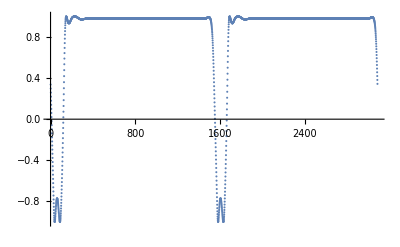

{{147},{148},{149},{221},{222},{223},{224},{225},{226},{227},{228},{229},{230},{231},{232},{233},{234},{235},{236},{1690},{1691},{1764},{1765},{1766},{1767},{1768},{1769},{1770},{1771},{1772},{1773},{1774},{1775},{1776},{1777},{1778}}

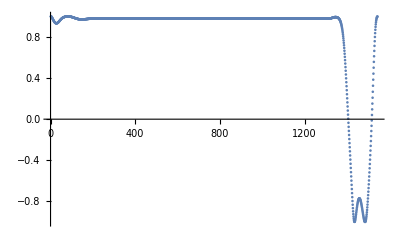

data/chimera2_rel.dat

```mathematica
ListPlot[out2[[All,1]],PlotRange->All]
Position[out2[[All,1]],u_/;u>0.999]
out3=out2[[147;;1690]];
ListPlot[out3[[All,1]],PlotRange->All]
Export["data/chimera2_rel.dat",Table[Prepend[out3[[i]],0.1*(i-1)],{i,1,Length[out3]}]]
```

```mathematica
Manipulate[ListPlot[{ArcTan[out3[[n,1;;M-1]],out3[[n,M-1+1;;2*(M-1)]]],ArcTan[out3[[n,2*(M-1)+1;;2*(M-1)+M]],out3[[n,2*(M-1)+M+1;;2*(M-1)+2*M]]]},PlotRange->{-Pi,Pi}],{n,1,Length[out3],1}]
```